# DimerModels

Author:	 Jens Forsgård
Latest version:	 12 July 2020

```mathematica
BeginPackage[ "DimerModels`"];
Needs["ComputationalGeometry`"];
```

```mathematica
HalfGraphGenus::usage = "HalfGraphGenus[ graph] returns the genus of the surface in which the graph is canonically embedded.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

TwistHalfGraph::usage = "TwistHalfGraph[ graph] returns the twisted half graph.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

InvoluteHalfGraph::usage = "InvoluteHalfGraph[ graph] returns the half graph with the same underlying graph as the input, but which is embedded in the involuted surface.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

IsomorphicHalfGraphsQ::usage = "IsomorphicHalfGraphsQ[ graph1, graph2] tests if there is an isomorphism between the two half-graphs.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

HalfGraphIsomorphismClasses::usage = "HalfGraphIsomorphismClasses[ list] partitions a list of half-graphs into isomorphism classes.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

ToGraph::usage = "ToGraph[ graph] returns the underlying graph of the half-graph.
N.B., the input should be given in half-graph notation: graph = (σ, τ), where σ and τ are permutaions of a set of half-edges."

Dimers::usage = "Dimers[ A] returns the list of all minimally consisten dimer models whose characteristic polygon is the conves hull of the columns of the (integer) matrix A."
```

```mathematica
Begin["Private`"];
```

### Comments

The main function is 'Dimers', which take a points configuration as input and gives a list of all associated minimally consistent dimer models on the two torus as output. Here, 'associated' means that the toric diagram of the dimer models is the convex hull N of the point set. In particular, it suffices to pass the vertices of the polygon as input.

The output graphs are given in half-edge notation. That is, a graph is of the form
	G = (σ, τ)
where H is a set of half-edges (motted in the notation), σ: H -> H is an involution without fixed points (identifying which pairs of half-edges are glued to an edge in the graph), and τ: H -> H is a permutaion (whose orbits are the vertices of the graph). See Bockland's 'A Dimer ABC' for more details.

A minimally consistent dimer model refers to a dimer model with toric diagram N which has the minimal number of vertices amongst all dimer models with toric diagram N. This condition is stronger or equivalent to any notion of consistent dimer model appearing in the literature.

The algorithm is based on the following observations.

Let N be a polygon and let G be a dimer model with diagram N. Let V be a smooth punctured Riemann surface with Newton polytope N, so that the twisted dimer model G^† is embedded in V. It follows that the faces of  G^† corresponds to the punctures of V. The punctures of V, in turn, corresponds to primitive edge segments (herefrom simply called punctures, to avoid confusion) of the polygon N. Hence, the vertices of the dual quiver graph (G^†)* corresponds to edges of the polygon N. Moreover, by the consistency condition, the number of oriented edges of the quiver graph (G^†)* connecting two vertices equals the determinant of the two punctures.

Let us form a characteristic cycle C as follows. Mark a point (representing a puncture) on each primitive edge segment of N. Draw oriented segments between any two punctures, counterclockwise along the boundary of N, according to the corresponding determinant. Since N is a polygon, the oriented segments glue together to form the closed cycle C. It is a simple exercise to show that the winding number of C along the boundary of N equals the number of white (or black) vertices in a minimally consistent domer model with characteristic polygon N. In particular, each white vertex of the dimer model G (and, hence, each face of (G^†)*) corresponds to a subcycle of the characteristic cycles of winding number one. That is, the set of white vertices (respectively the set oc black vertices) of the dimer mode G is obtained as a partitioning of the characteristic cycle C.

There is only finitely many partitionings of the characteristic cycle into subcycles of winding number one. Each such partition gives a possible set of (white or black) faces of the dual quiver (G^†)*. These whould be glues together to form the quiver graph (G^†)*, and there is only finitely many ways of glueing them. 

When glueing two partitions of the characteristic cycle to obtain a quiver graph H, then we always obtain a dimer model (as the dual of H) in the sense of a bipartite graph embedded in an orientable (possibly degenerate) surface. It is not, however, given that we obtain a dimer model embedded in V whose flip is contained in the real two torus. However, the only thing we need to check is that the genera are correct. Indeed, of the genera are correct, then by construction we obtain a dimer model (as the twist of the dual of H) on the real two torus whose characteristic diagram is N.

The algorithm takes the following steps.
  (1) Compute all possible partitions of the characteristic cycle.
  (2) Construct all possible glueings of two partitions. 
  (3) Discard any glueings which gives Riemann surfaces with the wrong genera.
  (4) Filter out isomorphic dimer models, to reduce the size of the output.

The reader will recognize that the algorithm is brute force. The slowest parts of the algorithm are steps (2) and (4). Especially in cases when N has many parallel primitive edge segments, the number of possible glueings tends to grow quite large. Still, the number of isomorphic dimer models stays quite modest. It would be preferrably if one could filter out some partitions of the characteristic cycle already after step (1). Indeed, it is definitely so that not all partitions of the characteristic cycle appears in a glueing which gives a dimer model with characteristic polygon N. However, as of this writing, no clear pattern has been identified.

### Auxiliary Functions

```mathematica
PolygonEdges[A_] := Module[{SplitVector, OrderedBoundaryPoints, BoundaryVectors},
	SplitVector[v_] := Module[{n = GCD @@ v}, ConstantArray[v/n, n]];
	OrderedBoundaryPoints = A[[ ConvexHull[A] ]];
	BoundaryVectors = Append[OrderedBoundaryPoints, First[OrderedBoundaryPoints]] // Differences;
	Flatten[ SplitVector/@(BoundaryVectors), 1] // Return;
];
```

```mathematica
PolygonGenus[A_] := Module[{OrderedBoundaryPoints, area, edges, boundary},
	(* Determined using Pick's formula. *)
	OrderedBoundaryPoints = A[[ ConvexHull[A] ]];
	area = OrderedBoundaryPoints // Polygon // Area;
	edges = Append[OrderedBoundaryPoints, First[OrderedBoundaryPoints]] // Differences;
	boundary = ( (GCD@@#) &/@ edges ) // Total;
	1 + area  - boundary/2 // Return;
];
```

```mathematica
MultiSubsets[list_, integer_] := Module[{k, Extensions, CompleteList, multisubsets},

	Extensions[multisubset_, element_] := Module[ {difference},
		difference = integer - Length[multisubset];
		Return[ Join[multisubset, ConstantArray[element, #]]&  /@  Range[0, difference] ];
	];
	
	CompleteList[multisubset_, element_] := Module[ {difference},
		difference = integer - Length[multisubset];
		Return[Join[multisubset, ConstantArray[element, difference]]];
	];
	
	multisubsets = ConstantArray[First[list], #] & /@ Range[0, integer];  
	k = 2;
	While[ k <  Length[list],
		multisubsets = Flatten[Extensions[#, list[[k]]]& /@ multisubsets, 1];
		k = k + 1;
	];
	Return[CompleteList[#, Last[list]] & /@ multisubsets ];
];
```

```mathematica
PermutationRules[list_] := Thread[list -> #]&  /@  Permutations[list];
```

```mathematica
RearrangeCycle[cycle_, element_] := Module[{position},
	position = Position[cycle, element] // First // First;
	Join[ Drop[cycle, position],  cycle[[1;;position]] ] // Return;   
];
```

```mathematica
LexiographicSuccessor[list_, maximums_] := Module[{length, difference, index, rules},

	LexiographicSuccessor::length = "The two lists are not equal in length.";
	LexiographicSuccessor::maxumum = "The list `1` is larger than `2` in at least one component.";
	LexiographicSuccessor::equal = "The list `1` has no successor smaller or equal to `2`.";           

	length = Length[list];
	If[ Length[maximums] ≠ length, Message[LexiographicSuccessor::length]; Return[$Failed];];
	difference = maximums - list;
	If[ Min[difference] < 0, Message[LexiographicSuccessor::maxumum, list, maximums]; Return[$Failed];];
	If[ Max[difference] == 0, Message[LexiographicSuccessor::equal, list, maximums]; Return[$Failed];];
	index = Position[ Sign /@ difference,  1]  // Flatten // Max;
	rules = Append[Thread[Range[index + 1, length] -> 1], index -> list[[index]] + 1];
	ReplacePart[list, rules] // Return;
];
```

### Graphs in Halfe-Edge notation

```mathematica
HalfGraphGenus[graph_]:=Module[{halfEdgesSet, rules, faces, genus},
	faces = (PermutationProduct@@(Cycles/@graph)) // First // Length;
	Return[(2-faces-Length[Last[graph]]+Length[First[graph]]) / 2 ];
];
```

```mathematica
TwistHalfGraph[graph_] := Module[{FlipOneNode},
	FlipOneNode[list_] := If[OddQ[First[list]], Return[Reverse[list]], Return[list]];
	Return[{First[graph], FlipOneNode/@Last[graph]}];
];
```

```mathematica
InvoluteHalfGraph[graph_] := Module[{k, white, black},
	Return[{First[graph], Reverse /@ Last[graph] }];
];
```

```mathematica
IsomorphicHalfGraphsQ[graph1_, graph2_] := Module[
	{K, edges, vertices1, vertices2, IsomorphismQ, ConsistentVertexDegreesQ, 
	ConsistentRulesQ, RulesInducedFromVertices, RulesInducedFromEdges, PossibleRules, m},
	
	IsomorphicHalfGraphsQ::input = "Edges of at least one input is not in the expected format: {{1,2},{3,4},...,{2K-1,2K}}.";
	
	(* STEP 1. INITIATION AND TYPE HANDLING *)K = Length[First[graph1]];If[ Length[First[graph1]] ≠ K, Return[False]; ];
	edges = Table[{2k-1, 2k}, {k,1,K}];
	If[First[graph1] ≠ edges || First[graph2] ≠ edges,
		Message[IsomorphicHalfGraphsQ::input]; 
		Return[$Failed];
	];
    vertices1 = Last[graph1];
    vertices2 = Last[graph2];
    If[Sort[Length /@ vertices1] ≠ Sort[Length/@vertices2],  Return[False];];

	(* INTERMEZZO: LOCAL FUNCTIONS *)
	IsomorphismQ[rules_] := Module[{rearrangedvertices1, rearrangedvertices2},
		rearrangedvertices1 = Sort[RearrangeCycle[#, Min[#]] &/@  vertices1,         First[#1] < First[#2] &];
		rearrangedvertices2 = Sort[RearrangeCycle[#, Min[#]] &/@ (vertices2/.rules), First[#1] < First[#2] &];
		Return[rearrangedvertices1 == rearrangedvertices2]
	];
	
    ConsistentVertexDegreesQ[rules_]:= Module[{CheckIndividualRule},
		CheckIndividualRule[rule_] := Module[{degree1, degree2},
			degree1 = Select[vertices1, MemberQ[#, Last[rule] ]& ] // First // Length ;
			degree2 = Select[vertices2, MemberQ[#, First[rule]]& ] // First // Length ;
			Return[degree1 == degree2];
		];
        AllTrue[rules, CheckIndividualRule] // Return;
	];

    ConsistentRulesQ[rules_] := Module[{counts},
		counts = Last /@  Join[  Tally[First /@ rules], Tally[Last /@ rules]  ];
		Return[Max[counts] == 1];
    ];

    RulesInducedFromVertices[rules_]:= Module[{RulesInducedFromOneRule},
		RulesInducedFromOneRule[rule_] := Module[{cycle1, cycle2},
			cycle1 = RearrangeCycle[  Select[vertices1, MemberQ[#, Last[rule] ]& ] // First,  Last[rule] ];
			cycle2 = RearrangeCycle[  Select[vertices2, MemberQ[#, First[rule]]& ] // First,  First[rule]];
			Thread[cycle2 -> cycle1] // Return ;
        ];
        RulesInducedFromOneRule /@ rules  // Flatten // DeleteDuplicates // Return ;
	];

	RulesInducedFromEdges[rules_]:=Module[{Interchange, sourcelabels, targetlabels},
        Interchange[n_] := If[ OddQ[n],  n + 1,  n - 1 ];
        sourcelabels = Interchange /@ (First /@ rules);
        targetlabels = Interchange /@ (Last  /@ rules);
        Join[rules, Thread[sourcelabels -> targetlabels]]  //  DeleteDuplicates  // Return ;
    ];

	(* PART 2: SEARCH FOR AN ISOMORPHISM *)
	(* Testing all possible relabelling unnecessary too expensive; if we guess the new label of one half-edge, 
	   then the labels of all other half-edges are determined by connectedness of the two graphs.  *)
    PossibleRules  = Table[ {1 -> k}, {k, 1, 2K} ];
    PossibleRules  = Select[PossibleRules, ConsistentVertexDegreesQ];    
    m = 0; (* Count the number of iterations for good measure *)
    While[ PossibleRules ≠ {}   &&   m < 4K,
        If[MemberQ[IsomorphismQ /@ PossibleRules, True], Return[True]; ];
        PossibleRules  = RulesInducedFromVertices /@ PossibleRules;
        PossibleRules  = RulesInducedFromEdges    /@ PossibleRules;
        PossibleRules  = Select[PossibleRules, ConsistentRulesQ];
        PossibleRules  = Select[PossibleRules, ConsistentVertexDegreesQ];
        m = m + 1;
    ];
    If[PossibleRules == {}, Return[False], Return[$Failed]];
];
```

```mathematica
HalfGraphIsomorphismClasses[GraphList_] := Gather[ Range[Length[GraphList]],  IsomorphicHalfGraphsQ[GraphList[[#1]], GraphList[[#2]]]& ];
```

```mathematica
ToGraph[graph_] := Module[{halfEdgesSet, rules, faces, genus},
	edges = First[graph];
	vertices = Last[graph];
	TranslateOneEdge[edge_] := UndirectedEdge[ Position[vertices, First[edge]] // First // First,  Position[vertices, Last [edge]] // First // First  ];
	Return[TranslateOneEdge /@ edges];
];
```

### Constructors

```mathematica
EdgeGroupsAndFaceSets[A_] := Module[
	{dualvertices, circumference, pairsofindices, determinants, halfedges,
	SetToCharacteristicList, ConsistentOrientationQ, caracteristiclists,
	PartitionsUpToCoordinate, partitions, k, detsums, halfedgesbygroup, 
	TranslatePartition, SortCycle, SortCycles},
	
	(* STEP 1:  INITIATION  *)
    (* Retrieve the primitive facet vectors of the boundary of the Newton polytope and count them. *) 
    (* Recall that each primitive facet vector corresponds to a vertex of the flipped dimer model; we call them dual vertices. *)
    dualvertices   = PolygonEdges[A];
    circumference  = Length[dualvertices];
    pairsofindices = Subsets[Range[circumference], {2}];
    determinants   = Det[ dualvertices[[#]] ]&  /@  pairsofindices;
    pairsofindices = MapAt[ Reverse,  pairsofindices,   Position[Sign /@ determinants, -1]  ];
    determinants   = Abs /@ determinants;
    halfedges      = Flatten[ (ConstantArray @@ #)& /@ Thread[{pairsofindices, determinants}], 1];  
  
  (* STEP 2:  CONSTRUCT A LIST OF ALL CLOSED SUBCYCLES OF WINDING NUMBER ONE OF THE CHARACTERISTIC CYCLE *)
    SetToCharacteristicList[halfedges_] := Module[{dilations},
        dilations = Sort /@ Thread[{halfedges, RotateLeft[halfedges]}];
        Return[ If[ MemberQ[dilations, Sort[#]], 1, 0] & /@ pairsofindices ]    
    ];
  
    ConsistentOrientationQ[characteristiclist_] := Module[{appearingedges},
        appearingedges = pairsofindices[[#]]& /@ Flatten[Position[characteristiclist, 1]];
        Return[ Sort[ First /@ appearingedges ] == Sort[ Last /@ appearingedges ] ];
    ];

    caracteristiclists = SetToCharacteristicList  /@  Subsets[Range[circumference], {3, circumference}];
    caracteristiclists = Select[caracteristiclists, ConsistentOrientationQ];
    
	(* STEP 3:  CONSTRUCT A LIST OF ALL PARTITIONS OF THE CHARACTERISTIC CYCLE INTO CYCLES OF WINDING NUMBER ONE  *)

    PartitionsUpToCoordinate[cycleList_, index_] := Module[{difference, admissible, multisubsets},
		(* Compute the difference of the sum of the cycles and the dets vector at position index.
		   If the numbers agree, then the trivial extension is the only extensions. *)
        difference = (determinants - Total[cycleList])[[index]];
        If[difference == 0, Return[{cycleList}]];
        admissible = Select[ caracteristiclists,   FirstPosition[#, 1] == {index}  & ];
        If[Length[admissible] == 0, Return[{}]];
        multisubsets = MultiSubsets[admissible, difference];
        Join[cycleList, #]& /@ multisubsets  //  Return;
    ];

    partitions = {{}}; 
    k = 1;
    While[k ≤ Length[determinants],
        partitions = Flatten[  PartitionsUpToCoordinate[#, k]&  /@  partitions,  1];
        partitions = Select[partitions,   Min[determinants - Total[#]] ≥ 0  &] // DeleteDuplicates;
        k = k + 1;
    ];
     
    partitions = Select[partitions, Total[#] == determinants &]; 

	(* STEP 4:  RELABEL THE RESULT. *)
    detsums = Total[determinants[[1 ;; #]]]& /@ Range[0, Length[determinants]];
    halfedgesbygroup = Table[Range[detsums[[k]] + 1, detsums[[k+1]]], {k, 1, Length[determinants]}];
    
    TranslatePartition[partition_] := Module[{RemainingIndices, HalfEdgeCycles, RemainingParts, positions},
        RemainingParts    = partition;
        RemainingIndices  = halfedgesbygroup;
        HalfEdgeCycles    = {};
        While[Length[RemainingParts] > 0,
            positions = Flatten[ Position[ First[RemainingParts], 1] ];
            HalfEdgeCycles = Append[ HalfEdgeCycles,  First /@ RemainingIndices[[positions]] ];
            RemainingIndices = Delete[RemainingIndices, {#, 1} & /@ positions];
            RemainingParts   = Drop[ RemainingParts, 1]; 
        ];
        Return[HalfEdgeCycles];
   ];
  
   partitions = TranslatePartition /@ partitions;  

  (* STEP 5:  SORT THE PARTITIONS. *)
    SortCycle[cycle_] := Module[{NextIndex, answer},
        NextIndex[index_] := Select[cycle, First[halfedges[[#]]] == Last[halfedges[[index]]] & ]  //  First;
        answer = {First[cycle]};
        While[Length[answer] < Length[cycle],
            answer = Append[answer, NextIndex[Last[answer]]];
        ];
        answer // Return;
    ];

    SortCycles[list_] := SortCycle /@ list;

    (* RETURN *)
    Return[{halfedgesbygroup, SortCycles /@ partitions}]
];
```

```mathematica
GraphsWithPrescribedGenera[white_, black_, genus_] := Module[{K, edges, graphlist},
    K = white // First // Flatten // Length;
	edges = Table[ {2k - 1, 2k}, {k, 1, K} ];
    graphlist = Flatten[ Table[ {edges, Join[w, b]}, {w, white}, {b, black}], 1];
    graphlist = Select[graphlist, HalfGraphGenus[#] == genus && HalfGraphGenus[TwistHalfGraph[#]] == 1 &];
    Return[ graphlist ];
];
```

### Main function: ComputeDimers

```mathematica
Options[Dimers] = 
	{
	 "Output"         -> False,
	 "FindOne"        -> False,
	 "StartAt"        -> 1,
	 "StopAt"         -> 0
	};
	
Dimers[A_, OptionsPattern[]] := Module[
    {genus, groupededges, vertexsets, adjustedgroupededges, permutations, multiplicities, edges,
    reversedvertexsets, white, black, graphlist, indexvector, rules, currentposition},
    (* Compute the genus of the associated Riemann surface *)
    genus =  PolygonGenus[A];
    (* Retrieve the EdgeGroups and the FaceSets *)
    {groupededges, vertexsets} = EdgeGroupsAndFaceSets[A];  
    If[OptionValue["Output"],  Print["Number of possible vertex sets is ", Length[vertexsets], "."]];
    (* Retrieve the list of permutations of half-edges associated to the same pairs of edges. *)
    permutations   = PermutationRules /@ Select[groupededges, Length[#] > 1 &];
    multiplicities = Length /@ permutations;
	(* Create the list of edges of the dimer model *)
	edges = Table[ {2k - 1, 2k}, {k, 1, Length[Flatten[groupededges]]} ];
    (* Consider two separate cases: whether there are permutations to take into account or not. *)
    If[ Length[multiplicities] == 0, 
        If[ OptionValue["Output"],  Print["Total number of graphs is ", Length[vertexsets]^2, "."];];
        reversedvertexsets = (Reverse /@ # &) /@ vertexsets;
        white = (2# - 1 &  /@ #)&  /@  vertexsets;
        black = (2#     &  /@ #)&  /@  reversedvertexsets;
        graphlist = GraphsWithPrescribedGenera[white, black, genus];
        If[OptionValue["FindOne"], Return[ First[graphlist] ] ];
        graphlist = graphlist[[  First /@ HalfGraphIsomorphismClasses[graphlist] ]];,
  (* ElseIf *)
        If[ OptionValue["Output"], Print["Total number of permutations is ", Times@@multiplicities, "."];];    
        (* Loop through all permutations *)
        indexvector = Append[ConstantArray[1, Length[multiplicities] - 1], 0] ;
        graphlist = {};
        currentposition = 1;
        While[ currentposition < OptionValue["StartAt"],
             indexvector     = LexiographicSuccessor[indexvector, multiplicities];      
             currentposition = currentposition + 1;
        ];    
        While[Total[indexvector] < Total[multiplicities],
            indexvector = LexiographicSuccessor[indexvector, multiplicities];
            rules       = permutations[[ #, indexvector[[#]] ]]&  /@  Range[Length[indexvector]]  // Flatten;
            reversedvertexsets = (Reverse /@ # &) /@ (vertexsets /. rules);
            white = (2# - 1 &  /@ #)&  /@  vertexsets;
            black = (2#     &  /@ #)&  /@  reversedvertexsets;
            graphlist = Join[graphlist, GraphsWithPrescribedGenera[white, black, genus ]];
            graphlist = graphlist[[  First /@ HalfGraphIsomorphismClasses[graphlist] ]];      
            If[ OptionValue["FindOne"] && (Length[graphlist] > 0), Return[ First[graphlist] ] ];
            If[ currentposition == OptionValue["StopAt"], Return[graphlist] ];
            currentposition = currentposition + 1;
        ];
    ];
    Return[graphlist];
];
```

```mathematica
End[];
EndPackage[];
```

Examples

### Example 1: Input/Output

Input is a list of points in the plane.
Output is a list of graphs in half-edge notaion. In this particular example, the output consists of one single graph.

```mathematica
A={{0,0},{1,0},{0,1},{1,1}};
Timing[Dimers[A]]
```

{0.007403,{{{{1,2},{3,4},{5,6},{7,8}},{{1,5,7,3},{4,8,6,2}}}}}

The edges of the graph are encoded by the permutation (which is an involution with no fixed points):
      { {1, 2}, {3, 4}, {5, 6}, {7, 8} }
The edges are always recorded in the above standard form.
 
The vertices are the ordbits of the permutation
      { {1, 5, 7, 3}, {4, 8, 6, 2} }
 
 For the coloring, "white" vertices are given by cycles containing only odd numbers and "black" vertices are given by cycles containing only even numbers.

### Example 2 a: Some remarks on isomorphisms

The algorithm filters dimer models up to orientation preserving isomorphisms.

```mathematica
A={{0,0},{1,0},{0,1},{1,2},{3,1}};
Timing[dimers = Dimers[A]]
```

{15.0812,{{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34}},{{1,25,13},{3,21,29,15},{5,23,33,17},{7,27,11},{9,31,19},{12,24,2},{20,26,4},{16,32,22,6},{18,30,8},{14,34,28,10}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34}},{{1,23,11},{3,25,13},{5,21,29,15},{7,31,17},{9,27,33,19},{20,26,2},{16,32,22,4},{18,34,24,6},{12,28,8},{14,30,10}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34}},{{1,25,13},{3,21,29,15},{5,23,33,17},{7,27,11},{9,31,19},{12,24,4},{20,26,6},{16,34,28,22,2},{18,32,8},{14,30,10}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34}},{{1,23,11},{3,25,13},{5,21,27,33,15},{7,29,17},{9,31,19},{20,26,6},{16,32,22,2},{18,34,24,4},{12,28,8},{14,30,10}}}}}

There might of course be graphs which are isomorphic if we allow an involution of the surface.

```mathematica
Table[ IsomorphicHalfGraphsQ[ dimer1, InvoluteHalfGraph[dimer2]], {dimer1, dimers}, {dimer2, dimers}]//MatrixForm
```

(False | True | False | False
True | False | False | False
False | False | False | True
False | False | True | False)

In this particular example, there are four non-isomorphic dimer models up to orientation preserving isomorphisms
But they appear as two pairs of dimer models which is isomorphic under involution.

### Example 2 b.

```mathematica
A={{1,0},{2,0},{3,1},{3,2},{2,1},{2,3},{2,2},{1,3}};
Timing[dimers = Dimers[A]]
```

{7.22815,{{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44}},{{1,15,41,7},{3,27,39,5},{9,23,31,17},{11,33,19},{13,37,21},{25,35,43,29},{6,36,14,2},{8,38,26,4},{20,42,28,10},{22,44,32,12},{18,40,16},{30,34,24}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44}},{{1,15,41,7},{3,27,39,5},{9,23,31,17},{11,33,19},{13,37,21},{25,35,43,29},{6,32,12,2},{8,34,24,4},{20,38,26,10},{18,36,14},{22,44,40,16},{30,42,28}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44}},{{1,15,41,7},{3,27,39,5},{9,25,35,43,19},{11,31,17},{13,37,21},{23,33,29},{6,36,14,2},{8,38,26,4},{22,44,32,24,10},{20,34,12},{18,40,16},{30,42,28}}}}}

```mathematica
Table[ IsomorphicHalfGraphsQ[ dimer1, InvoluteHalfGraph[dimer2]], {dimer1, dimers}, {dimer2, dimers}]//MatrixForm
```

(False | True | False
True | False | False
False | False | True)

In this exaple, we have one dimer models which is invariant under involution of the surface.

### Example 3 Complexity

Complexity is measured in the size of the producets of all determinants of pairs of primitive edge vectors of the Newton polytope.
This dependence on the input is not necessarily obvious.

Turn "Output" to True get an estimation of the number of cases.

```mathematica
A={{0,0},{1,0},{0,1},{1,2},{3,1}};
Timing[Dimers[A, "Output" ->  True];]
```

Number of possible vertex sets w/o is 4.

Total number of graphs is 9216.

{15.7959,Null}

The algorithm uses little memory. The main problem to overcome is the sheer number of cases to test.
Any person with sufficient provessing power and/or sufficient time is lucky in this respect.

There is a built in functionality to split up computations into several parts.

```mathematica
A={{0,0},{1,0},{0,1},{1,2},{4,1}};
Timing[dimers1  = Dimers[A, "Output" ->  True, "StartAt" -> 1, "StopAt" -> 10000];]
```

Number of possible vertex sets is 4.

Total number of permutations is 1244160.

{67.4893,Null}

The Start/Stop counter refers to the list of permutations.  For each permutation, the algorithm checks (no. poss. vertex sets)^2 graphs. 
That is, in the above example there is a total of   4^2  x  1 244 160  =  19 906 560  graphs to check, and we checked 4^2 x  10 000  = 160 000
graphs in the first batch.

Needless to say, if you subdivide into batches then the output lists should be joined and filtered for isomorphic graphs.

```mathematica
Timing[dimers2  = Dimers[A, "Output" ->  False, "StartAt" -> 10000, "StopAt" -> 20000];]
```

{121.397,Null}

```mathematica
dimers = Join[dimers1, dimers2];
dimers = dimers[[  First /@ HalfGraphIsomorphismClasses[ dimers ] ]]
```

{{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44},{45,46}},{{1,33,17},{3,35,19},{5,29,39,21},{7,31,45,23},{9,37,15},{11,41,25},{13,43,27},{16,32,2},{28,34,4},{26,36,6},{22,42,30,8},{24,40,10},{20,44,12},{18,46,38,14}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44},{45,46}},{{1,31,15},{3,33,17},{5,35,19},{7,29,39,21},{9,41,23},{11,43,25},{13,37,45,27},{28,34,2},{26,36,4},{22,42,30,6},{24,46,32,8},{16,38,10},{20,40,12},{18,44,14}}}}

This built in functionality causes the algorithm to be slightly slower than necessary, It is of course annoying to brute force through so many cases, 
when the number of non-isomorphic dimer models often stays in single digits. Improvements are welcome. It might definitely by that there are better 
ways of using the symmetries to reduce computing times than what is encoded into the algorithm so far.

### Example 4 Find one instance

If you are only interested in findin one dimer model, then we can speed things up significantly.

```mathematica
A={{0,0},{1,0},{0,1},{1,2},{3,1}};
Timing[Dimers[A, "FindOne" ->  True]]
```

{0.07233,{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34}},{{1,25,13},{3,21,29,15},{5,23,33,17},{7,27,11},{9,31,19},{12,24,2},{20,26,4},{16,32,22,6},{18,30,8},{14,34,28,10}}}}

If you are only interested in findin one dimer model, then we can speed things up.

```mathematica
A={{0,0},{1,0},{0,1},{1,2},{4,1}};
Timing[Dimers[A, "FindOne" ->  True]]
```

{8.28879,{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28},{29,30},{31,32},{33,34},{35,36},{37,38},{39,40},{41,42},{43,44},{45,46}},{{1,33,17},{3,35,19},{5,29,39,21},{7,31,45,23},{9,37,15},{11,41,25},{13,43,27},{16,32,2},{28,34,4},{26,36,6},{22,42,30,8},{24,40,10},{20,44,12},{18,46,38,14}}}}

### Example 5 Visualization

```mathematica
A={{0,0},{2,0},{0,1},{2,1},{1,2}};
Timing[dimers = Dimers[A]]
```

{0.100409,{{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28}},{{1,13,25,5},{3,19,27,7},{9,21,15},{11,23,17},{8,24,10,2},{6,22,4},{16,26,20,12},{18,28,14}}},{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24},{25,26},{27,28}},{{1,9,19,27,7},{3,21,5},{11,23,17},{13,25,15},{6,26,20,12,2},{8,24,4},{16,22,10},{18,28,14}}}}}

Translate to a graph in classical notation by the function ToGraph.

```mathematica
graph = ToGraph [ dimers // First ]
```

{1<->5,2<->6,1<->6,2<->5,3<->5,4<->7,1<->8,3<->7,4<->8,2<->7,3<->6,4<->5,1<->7,2<->8}

The graph can be visualized with Mathematicas built in functions for graphs.
Needless to say, the embedding into the orientable surface is seldom visible in the visualization.

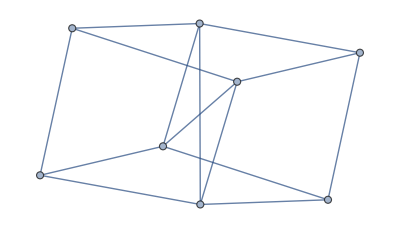

```mathematica
Graph[graph]
```